```mathematica
f[θ_,k_] :=Exp[θ*k]/(Exp[θ*k]+1)
```

```mathematica
Simplify[D[f[θ,k],k]]
```

(ⅇ^(k θ) θ)/((1+ⅇ^(k θ))^2)

```mathematica
h[ϵ_]:=PDF[GammaDistribution[2,2],ϵ]
```

```mathematica
g[ϵ_]:=-ϵ*h'[ϵ]-h[ϵ]
```

```mathematica
g[ϵ]
```

-(Piecewise[{{1/4 ⅇ^(-ϵ/2) ϵ, ϵ>0}, {0, True}}])-ϵ (Piecewise[{{0, ϵ<0}, {ⅇ^(-ϵ/2)/4-1/8 ⅇ^(-ϵ/2) ϵ, ϵ>0}, {Indeterminate, True}}])

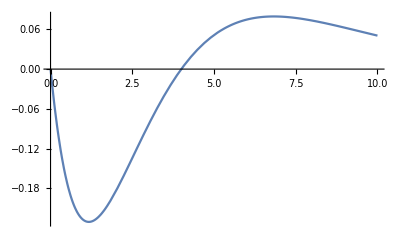

```mathematica
Plot[g[ϵ],{ϵ,0,10}]
```

```mathematica
Integrate[g[x],{x,0,Infinity}]
```

0

```mathematica
f[4.5,100000000]
```

1.

```mathematica
f[θ,k]
```

```mathematica
ⅇ^(k θ)/(1+ⅇ^(k θ))
```

ⅇ^(k θ)/(1+ⅇ^(k θ))

```mathematica
Limit[f[θ,k],k->Infinity]
```

ConditionalExpression[1, θ>0]

```mathematica
α=0.9
g[θ_,k_]:=Exp[θ*k^α]/(Exp[θ*k^α]+1)
```

0.9

```mathematica
g[θ,k]
```

(ⅇ^(k^0.9 θ))/(1+ⅇ^(k^0.9 θ))

```mathematica
Limit[f[θ,k],k->Infinity]
```

ConditionalExpression[1, θ>0]

```mathematica
f2[θ_,k_]:=Exp[θ*k]/(Exp[θ*k]+1)-0.1
```

```mathematica
f2[θ,k]
```

-0.1+ⅇ^(k θ)/(1+ⅇ^(k θ))

```mathematica
Limit[f2[θ,k],k->Infinity]
```

ConditionalExpression[0.9, θ>0]

```mathematica
f2[0.8,0]
```

0.4